# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Entropy

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\QMB_offline.wl"]
```

```mathematica
Needs["MaTeX`"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Random product states analysis

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Chop[Tr[rho.rho]];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}
];
Clear[sdiag];
sdiag[ini_]:=Module[{state=Dyad[Conjugate[eigenvec].ini],rho,λ},
rho=MatrixPartialTrace[state,1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
L=6;
g=J=1;
h=0.5;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
scaledeigenval=Rescale[eigenval+Abs[eigenval[[1]]]];
colors=Table[Blend[{Blue,Red},i],{i,scaledeigenval}];
custom[x_]:=Blend[{Blue,Red},x];
```

```mathematica
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
entropies=ParallelTable[svn[i,0],{i,eigenvec}];
```

```mathematica
data=ParallelTable[{{scaledeigenval[[i]],Chop[entropies[[All,1]]][[i]]}},{i,Length[eigenval]}];
data2=ParallelTable[{{scaledeigenval[[i]],Chop[entropies[[All,2]]][[i]]}},{i,Length[eigenval]}];
```

```mathematica
ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->800,PlotLegends->BarLegend[{custom,{Min[scaledeigenval],Max[scaledeigenval]}},LegendLabel->"Energy"]]
ListPlot[data2,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{l}",FontSize->35],Black]},ImageSize->800,PlotLegends->BarLegend[{custom,{Min[scaledeigenval],Max[scaledeigenval]}},LegendLabel->"Energy"]]
```

-Graphics-

-Graphics-

```mathematica
randoms=Table[RandomChainProductState[L],{i,2000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=Table[Chop[Conjugate[i].H.i],{i,randoms}];
rescaledNewValues=Rescale[energies,MinMax[eigenval],{0,1}];
```

```mathematica
entropydiag=ParallelTable[sdiag[i],{i,randoms}];
```

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,rescaledNewValues}];
info=Table[{{iprs[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[rescaledNewValues],Max[rescaledNewValues]}},LegendLabel->"Energy"]]
```

-Graphics-

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,rescaledNewValues}];
info=Table[{{iprs[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[rescaledNewValues],Max[rescaledNewValues]}},LegendLabel->"Energy"]]
```

-Graphics-

```mathematica
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tf=1000;
tlist=Range[0,tf,Δt];
```

```mathematica
sortedrandoms=SortBy[Transpose[{Chop[entropydiag],randoms}],First];
```

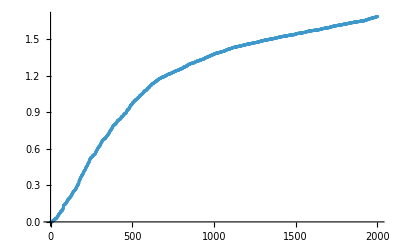

```mathematica
Sort[Chop[entropydiag]]//ListPlot
```

```mathematica
sdiag[sortedrandoms[[All,2]][[1]]]
sdiag[sortedrandoms[[All,2]][[-1]]]
```

0.000030003

1.68432

```mathematica
entropies=ParallelTable[svn[sortedrandoms[[All,2]][[-1]],t],{t,tlist},DistributedContexts->Full];
```

```mathematica
entro1=Transpose[{tlist,entropies[[All,1]]}];
entro2=Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))entropies[[All,2]]}];
```

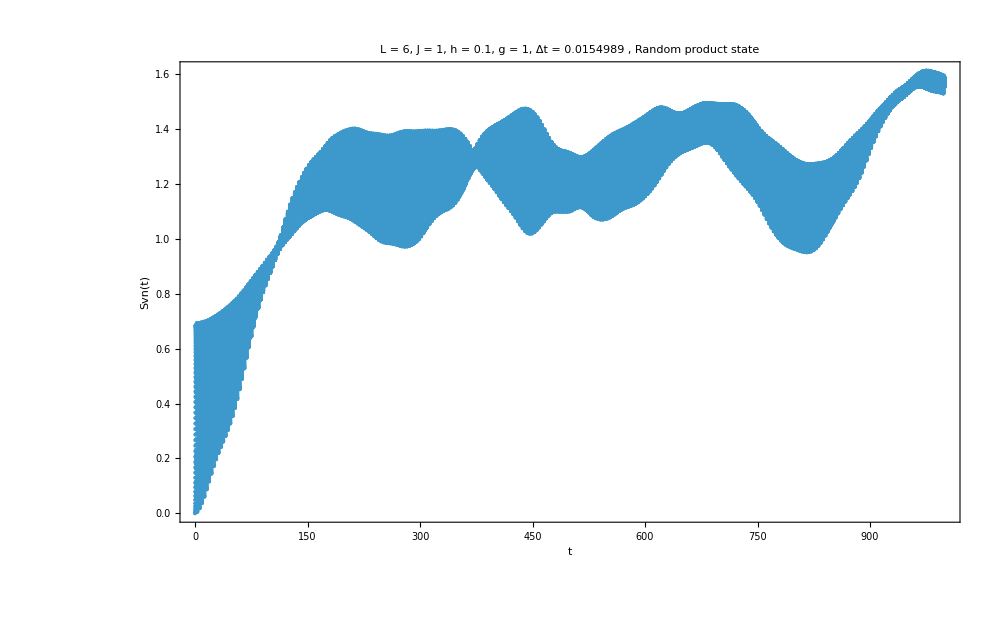

```mathematica
svnplots=ListPlot[entro1,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

```mathematica
entropies=ParallelTable[svn[sortedrandoms[[All,2]][[1]],t],{t,tlist},DistributedContexts->Full];
```

```mathematica
entro1=Transpose[{tlist,entropies[[All,1]]}];
entro2=Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))entropies[[All,2]]}];
```

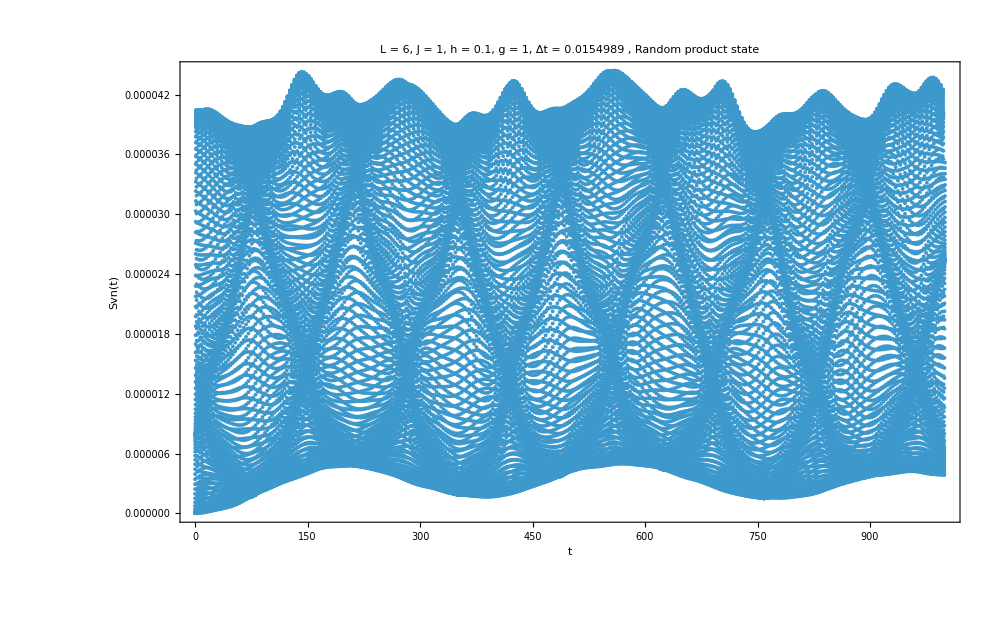

```mathematica
svnplots=ListPlot[entro1,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

# Random coherent states analysis

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Chop[Tr[rho.rho]];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}
];
Clear[sdiag];
sdiag[ini_]:=Module[{state=Dyad[Conjugate[eigenvec].ini],rho,λ},
rho=MatrixPartialTrace[state,1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
L=6;
g=J=1;
h=0.1;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
scaledeigenval=Rescale[eigenval+Abs[eigenval[[1]]]];
colors=Table[Blend[{Blue,Red},i],{i,scaledeigenval}];
custom[x_]:=Blend[{Blue,Red},x];
```

```mathematica
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
entropies=ParallelTable[svn[i,0],{i,eigenvec}];
```

```mathematica
data=ParallelTable[{{scaledeigenval[[i]],Chop[entropies[[All,1]]][[i]]}},{i,Length[eigenval]}];
data2=ParallelTable[{{scaledeigenval[[i]],Chop[entropies[[All,2]]][[i]]}},{i,Length[eigenval]}];
```

```mathematica
ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->800,PlotLegends->BarLegend[{custom,{Min[scaledeigenval],Max[scaledeigenval]}},LegendLabel->"Energy"]]
ListPlot[data2,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{l}",FontSize->35],Black]},ImageSize->800,PlotLegends->BarLegend[{custom,{Min[scaledeigenval],Max[scaledeigenval]}},LegendLabel->"Energy"]]
```

-Graphics-

-Graphics-

```mathematica
randoms=Table[coherentstate[RandomQubitState[],L],{i,2000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=Table[Chop[Conjugate[i].H.i],{i,randoms}];
rescaledNewValues=Rescale[energies,MinMax[eigenval],{0,1}];
```

```mathematica
entropydiag=ParallelTable[sdiag[i],{i,randoms}];
```

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,rescaledNewValues}];
info=Table[{{iprs[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, coherent\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[rescaledNewValues],Max[rescaledNewValues]}},LegendLabel->"Energy"]]
```

-Graphics-

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,rescaledNewValues}];
info=Table[{{iprs[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, coherent\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[rescaledNewValues],Max[rescaledNewValues]}},LegendLabel->"Energy"]]
```

-Graphics-

```mathematica
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tf=1000;
tlist=Range[0,tf,Δt];
```

```mathematica
sortedrandoms=SortBy[Transpose[{Chop[entropydiag],randoms}],First];
```

```mathematica
Sort[Chop[entropydiag]]//ListPlot
```

-Graphics-

```mathematica
entropies=ParallelTable[svn[sortedrandoms[[All,2]][[-1]],t],{t,tlist},DistributedContexts->Full];
```

```mathematica
entro1=Transpose[{tlist,entropies[[All,1]]}];
entro2=Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))entropies[[All,2]]}];
```

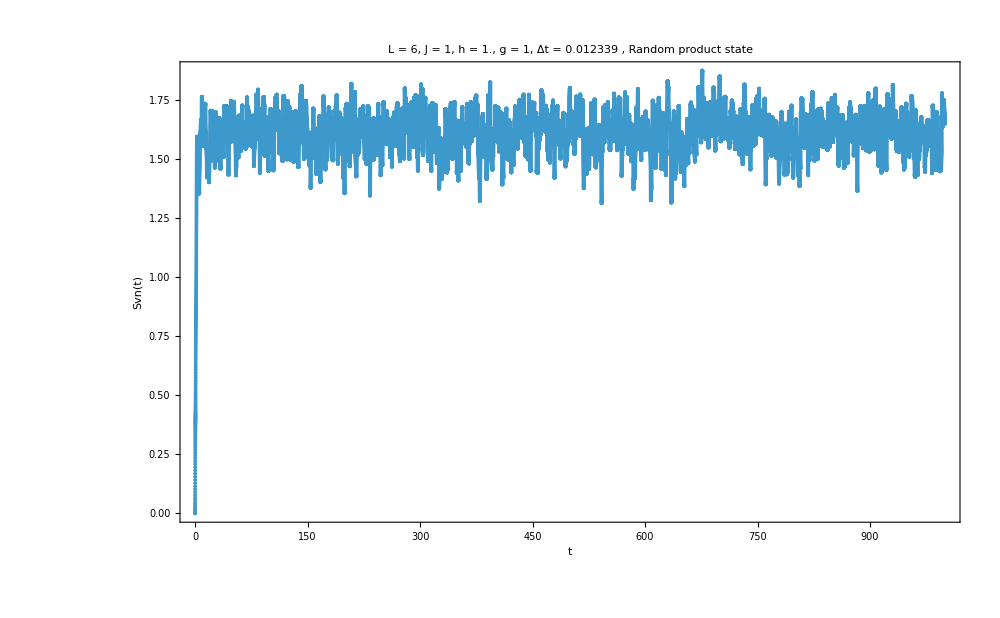

```mathematica
svnplots=ListPlot[entro1,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

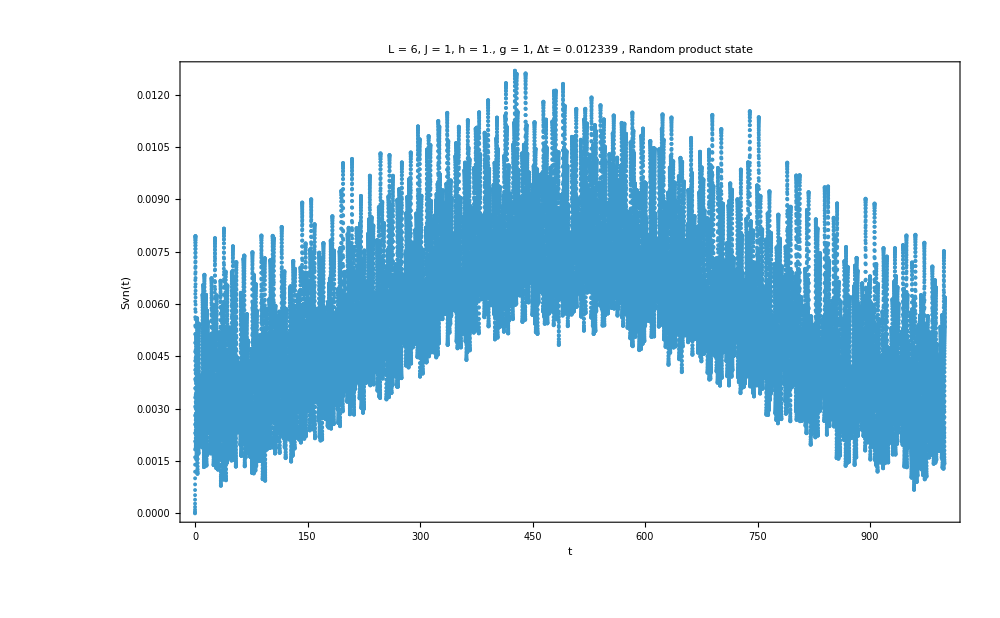

```mathematica
svnplots=ListPlot[entro1,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

# Several random states

## Open

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Chop[Tr[rho.rho]];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}
];
```

```mathematica
L=4;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
```

```mathematica
tlist=Range[0,(10),Δt];
tlist//Length
```

528

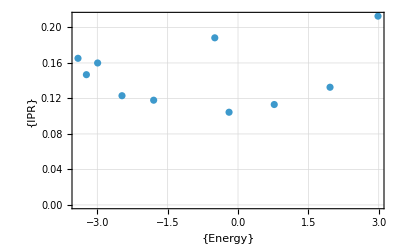

```mathematica
randoms=Table[RandomChainProductState[L],{i,10}];
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=Table[Chop[Conjugate[i].H.i],{i,randoms}];
ListPlot[Transpose[{energies,iprs}],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{{"Energy"},{"IPR"}}]
```

```mathematica
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
```

```mathematica
entro1=Table[Transpose[{tlist,entropies[[i]][[All,1]]}],{i,Length[randoms]}];
entro2=Table[Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))entropies[[i]][[All,2]]}],{i,Length[randoms]}];
```

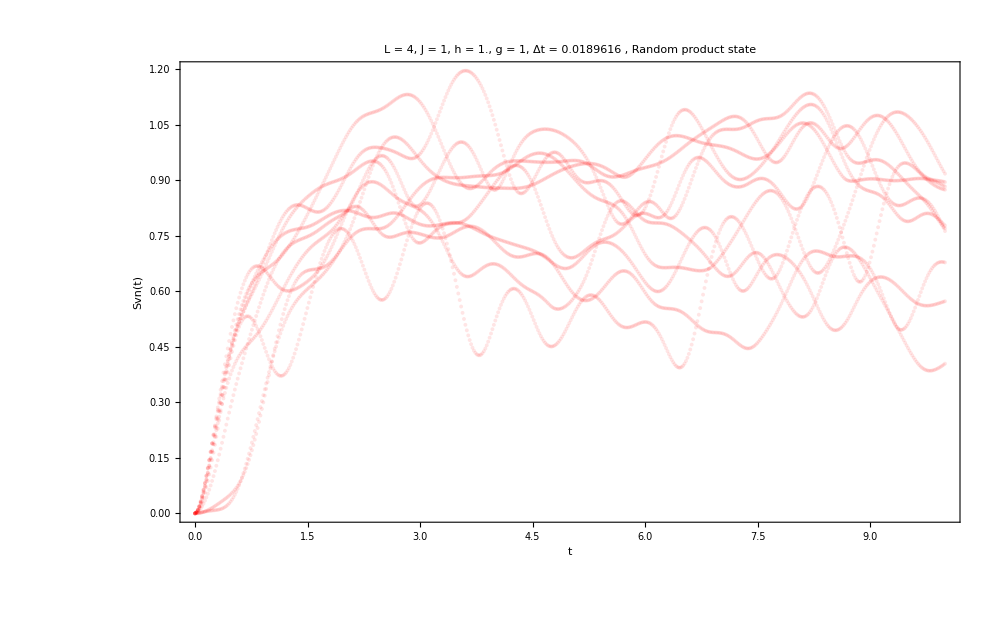

```mathematica
svnplots=ListPlot[entro1,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],PlotStyle->Directive[Red,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

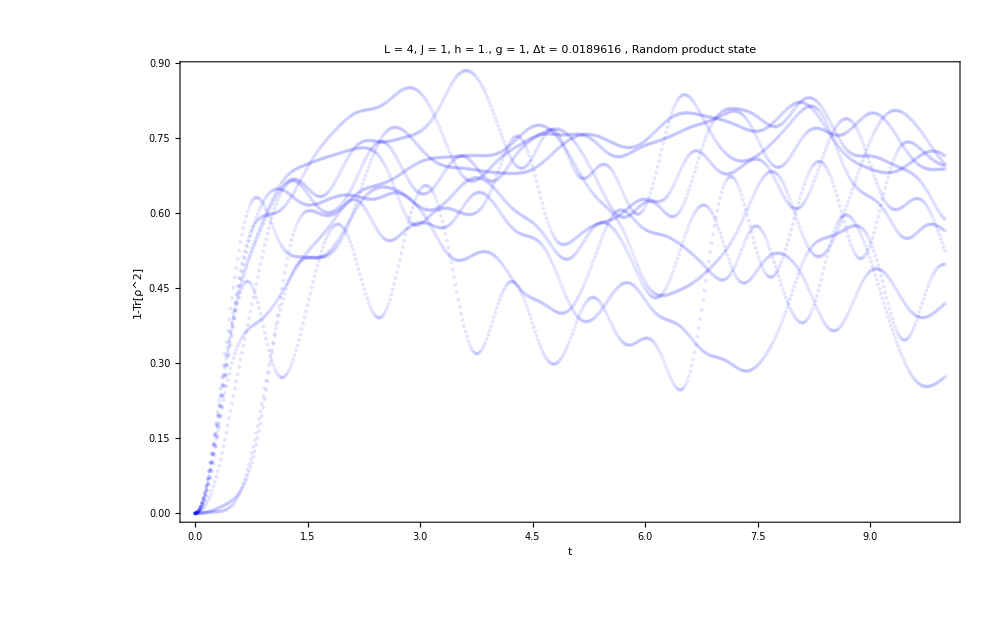

```mathematica
purityplots=ListPlot[entro2,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],PlotStyle->Directive[Blue,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["1-Tr[ρ^2]"]},PlotRange->All,ImageSize->1000]
```

# Results

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Tr[rho.rho];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-Chop[purity]}
];
Clear[sdiag];
sdiag[ini_]:=Module[{state=Dyad[Conjugate[eigenvec].ini],rho,λ},
rho=MatrixPartialTrace[state,1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
Clear[h,L];
(*I have data only for h=0.5,1*)
h=0.5;
J=g=1;
```

```mathematica
(*I have data for L = 4,6,8*)
L=4;
H=IsingNNOpenHamiltonian[h,g,J,L];
(*H=IsingNNClosedHamiltonian[h,g,J,L];*)
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
```

```mathematica
texts={"closed","open"};
text=texts[[1]];
Clear[data1];
```

```mathematica
data1=Import["D:\\INVESTIGACION\\2025\\PCS\\Entropy\\entropies_withpurity_L_"<>ToString[L]<>"_"<>ToString[text]<>"chain_10_randomstates_h_"<>ToString[h]<>".m"];
```

```mathematica
randoms=data1[[1]];
```

```mathematica
entro1=Table[Transpose[{tlist,data1[[2]][[i]][[All,1]]}],{i,Length[randoms]}];
entro2=Table[Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))data1[[2]][[i]][[All,2]]}],{i,Length[randoms]}];
```

```mathematica
meanssvn1=Table[Mean[i[[All,2]]],{i,entro1}];
meanspurity1=Table[Mean[i[[All,2]]],{i,entro2}];
diagonalentropies1=Table[sdiag[i],{i,randoms}];
```

```mathematica
(*This generates the plot of the comparison between the diagonal entropy and the time average for the 10 random initial states*)
```

```mathematica
fig1=ListPlot[{meanssvn1,diagonalentropies1},PlotTheme->"Detailed",Joined->True,PlotMarkers->Automatic,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" ,10 Random product state, "<>ToString[text]<>" chain",25,Black],PlotStyle->{Directive[Dashed,Black],Directive[Dashed,Red]},FrameLabel->{Style[MaTeX["i",FontSize->40],Black],Style[MaTeX["S",FontSize->40],Black]},FrameStyle->Directive[Black,FontSize->30],PlotRange->All,ImageSize->1000,PlotLegends->{Style[MaTeX["<S_{vn}>",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]}];
Export["entropycomparison_"<>ToString[text]<>"chain_L_"<>ToString[L]<>"_h_"<>ToString[h]<>".png",fig1,ImageResolution->400]
```

entropycomparison_closedchain_L_8_h_0.5.png

```mathematica
(*This generates the plots of the Svn(t) for the 10 initial states*)
```

```mathematica
Do[
svnplots1=Show[{ListPlot[entro1[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state, "<>ToString[text]<>" chain",20,Black],PlotStyle->Directive[Gray,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->40],Black],Style[MaTeX["S_{vn}(t)",FontSize->40],Black]},PlotRange->All,ImageSize->1000],Plot[{meanssvn1[[q]],diagonalentropies1[[q]]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Dashed,Black],Directive[Dashed,Red]},PlotLegends->{Style[MaTeX["<S_{vn}>",FontSize->30],Black],Style[MaTeX["S_{d}",FontSize->30],Black]}]},PlotRange->All];
Export["vnentropy_"<>ToString[text]<>"chain_L_"<>ToString[L]<>"_h_"<>ToString[h]<>"_state_"<>ToString[q]<>".png",svnplots1,ImageResolution->400];
,{q,10}]
```

```mathematica
(*This generates the plots of the Sl(t) for the 10 initial states*)
```

```mathematica
Do[
svnplots1=Show[{ListPlot[entro2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state, "<>ToString[text]<>" chain",20,Black],PlotStyle->Directive[Gray,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->40],Black],Style[MaTeX["1- Tr(\\hat{\\rho}_{B}^2)",FontSize->40],Black]},PlotRange->All,ImageSize->1000],Plot[meanspurity1[[q]],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Dashed,Black],Directive[Dashed,Red]},PlotLegends->{Style[MaTeX["S_{l}",FontSize->30],Black]}]},PlotRange->All];
Export["purity_"<>ToString[text]<>"chain_L_"<>ToString[L]<>"_h_"<>ToString[h]<>"_state_"<>ToString[q]<>".png",svnplots1,ImageResolution->400];
,{q,10}]
```